```mathematica
(*Бовт Тимофей 7 группа 7 вариант*)
(*1. Вычислить*)
```

```mathematica
{Exp[2],Pi^2,Log[2,7],2^30}
```

{ⅇ^2,π^2,Log[7]/Log[2],1073741824}

```mathematica
(*2. Разложить на множители*)
FactorInteger[{123456789123456789,25739445264}]
```

{{{3,2},{7,1},{11,1},{13,1},{19,1},{3607,1},{3803,1},{52579,1}},{{2,4},{3,1},{13,1},{41249111,1}}}

```mathematica
expr1=x^4+y^4+z^4-2 x^2 y^2-2 x^2 z^2-2 y^2 z^2;
expr2=(x+y+z)^3-x^3-y^3-z^3;

{Factor[expr1],Factor[expr2]}
```

{(x-y-z) (x+y-z) (x-y+z) (x+y+z),3 (x+y) (x+z) (y+z)}

```mathematica
(*3. Упростить*)
exprA=1/(1-x)+1/(1+x)+2/(1+x^2)+4/(1+x^4)+8/(1+x^8)+16/(1+x^16);
Simplify[exprA]
```

-32/(-1+x^32)

```mathematica
exprB=1/(x (x+1))+1/((x+1) (x+2))+1/((x+3) (x+2))+1/((x+3) (x+4))+1/((x+4) (x+5));
Simplify[exprB]
```

5/(5 x+x^2)

```mathematica
(*4. Решить уравнение*)
Solve[a x^10+x^2==0,x]
```

{{x→0},{x→0},{x→-(-1)^(1/8)/a^(1/8)},{x→(-1)^(1/8)/a^(1/8)},{x→-(-1)^(3/8)/a^(1/8)},{x→(-1)^(3/8)/a^(1/8)},{x→-(-1)^(5/8)/a^(1/8)},{x→(-1)^(5/8)/a^(1/8)},{x→-(-1)^(7/8)/a^(1/8)},{x→(-1)^(7/8)/a^(1/8)}}

```mathematica
Solve[x^3-3 x+2==0,x]
```

{{x→-2},{x→1},{x→1}}

```mathematica
(*5. Найти n-ую производную*)
D[Sin[x],{x,n}]
```

Sin[(n π)/2+x]

```mathematica
D[Cos[2x],{x,n}]
```

2^n Cos[(n π)/2+2 x]

```mathematica
D[1/(1+x),{x,n}]
```

(1+x)^(-1-n) FactorialPower[-1,n]

```mathematica
D[Exp[-3x],{x,n}]
```

(-3)^n ⅇ^(-3 x)

```mathematica
(*6. Вычислить интегралы*)
Integrate[Sqrt[3-2x-x^2],x]
```

1/2 (1+x) √(3-2 x-x^2)-4 ArcTan[(√(3-2 x-x^2))/(3+x)]

```mathematica
Integrate[x^5/(x+2),{x,-1,1}]
```

526/15-32 Log[3]

```mathematica
Integrate[Integrate[Log[Sqrt[x^2+y^2]],{x,-Sqrt[1-y^2],Sqrt[1-y^2]}],{y,-1,1}]
```

-π/2

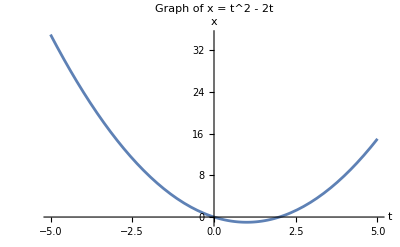

```mathematica
(*7. Построить графики следующих функций*)
Plot[t^2-2t,{t,-5,5},AxesLabel->{"t","x"},PlotLabel->"Graph of x = t^2 - 2t"]
```

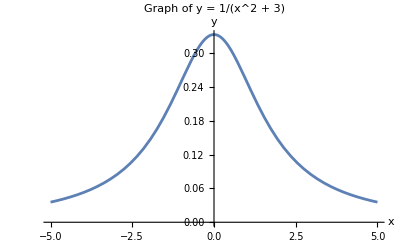

```mathematica
Plot[1/(x^2+3),{x,-5,5},AxesLabel->{"x","y"},PlotLabel->"Graph of y = 1/(x^2 + 3)"]
```

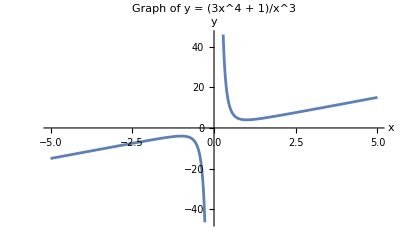

```mathematica
Plot[(3x^4+1)/x^3,{x,-5,5},AxesLabel->{"x","y"},PlotLabel->"Graph of y = (3x^4 + 1)/x^3"]
```

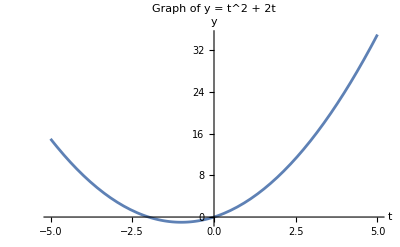

```mathematica
Plot[t^2+2t,{t,-5,5},AxesLabel->{"t","y"},PlotLabel->"Graph of y = t^2 + 2t"]
```

```mathematica
(*8. Дана матрица A=((1 2 3) (4 5 6) (7 8 9))
Найти собственные значения и собственные векторы этой матрицы.Решить систему уравнений Ax=b,где b=(1 1 1)*)
A={{1,2,3},{4,5,6},{7,8,9}};
{eigenvalues,eigenvectors}=Eigensystem[A]
```

{{3/2 (5+√33),-3/2 (-5+√33),0},{{-(-15-√33)/(33+7 √33),(4 (6+√33))/(33+7 √33),1},{-(15-√33)/(-33+7 √33),(4 (-6+√33))/(-33+7 √33),1},{1,-2,1}}}

```mathematica
b={1,1,1};
x=x/. NSolve[A.x==b,x]
```

Dot::dotsh: Tensors {{1,2,3},{4,5,6},{7,8,9}} and {InverseFunction[Dot,2,2][{{1,2,3},{4,5,6},{7,8,9}},1.]} have incompatible shapes.

{InverseFunction[Dot,2,2][{{1,2,3},{4,5,6},{7,8,9}},1.]}

```mathematica
(*9. Удалить из списка два последних значения
(1,0,7,9,6,3,2)*)
list={1,0,7,9,6,3,2};
newList=Drop[list,-2]
```

{1,0,7,9,6}

```mathematica
(*10. Найти условный max и min функции z= x+2y при условии x^2+y^2 = 5*)
f[x_,y_]:=x+2y;
constraint=x^2+y^2-5;
lagrangeMultiplier=Solve[{Grad[f[x,y]-λ constraint,{x,y}]=={0,0},constraint==0},{x,y,λ}];

{{xval,yval,λval}}=N[lagrangeMultiplier][[1]];

zmin=f[xval,yval];
zmax=f[-xval,-yval];

{{xval,yval},zmin,zmax}
```

Solve::ivar: {InverseFunction[Dot,2,2][{{1,2,3},{4,5,6},{7,8,9}},1.]} is not a valid variable.

Solve::ivar: {InverseFunction[Dot,2,2][{{1.,2.,3.},{4.,5.,6.},{7.,8.,9.}},1.]} is not a valid variable.

Set::shape: Lists {{xval,yval,λval}} and {{=={0.,0.},{-5.+y^2+(InverseFunction[Dot,2,2][{{«3»},{«3»},{«3»}},1.])^2}==0.} are not the same shape.

{{xval,yval},xval+2 yval,-xval-2 yval}